```mathematica
Needs["MaTeX`"];
SetDirectory[NotebookDirectory[]]
```

/Users/mcmcclur/Documents/html/classes/Spring2020CalcIII/online_presentations/04.21.LineIntegrals/images

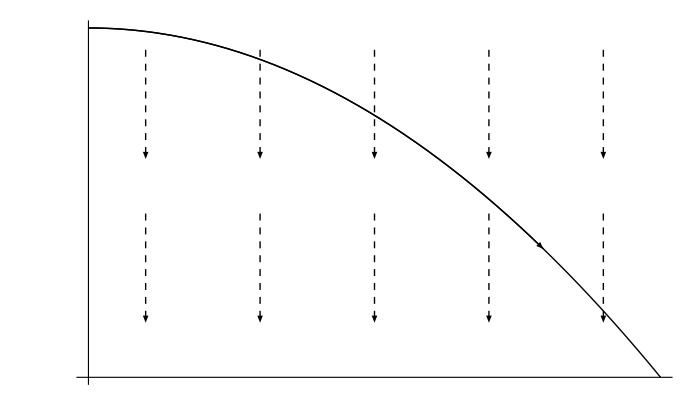

```mathematica
pic0 = ParametricPlot[{10t,64-16t^2},{t,0,2},AspectRatio->0.6,PlotStyle->{Thick,Black}];
pts = Cases[pic0,Line[pts_] :> pts[[;;126]],Infinity];
gravity = Table[Arrow[{{x,y},{x,y-20}}],{x,2,20,4},{y,30,60,30}];
ticks = {Table[{x,MaTeX[x]},{x,4,20,4}], Table[{y,MaTeX[y]},{y,20,60,20}]};
trajectory = Show[pic0,Epilog->{Arrow[pts], Dashed,Arrowheads[0.015],gravity},ImageSize->700,
Ticks -> ticks]
```

```mathematica
Export["parabolicTrajectory.png", trajectory]
```

parabolicTrajectory.png

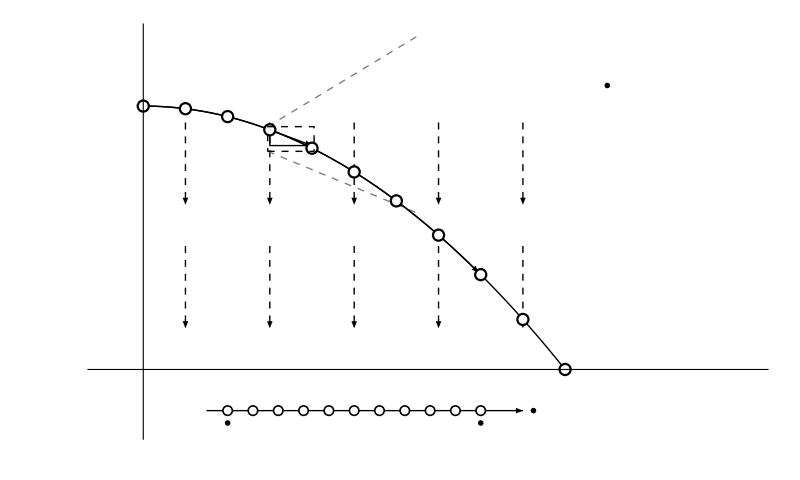
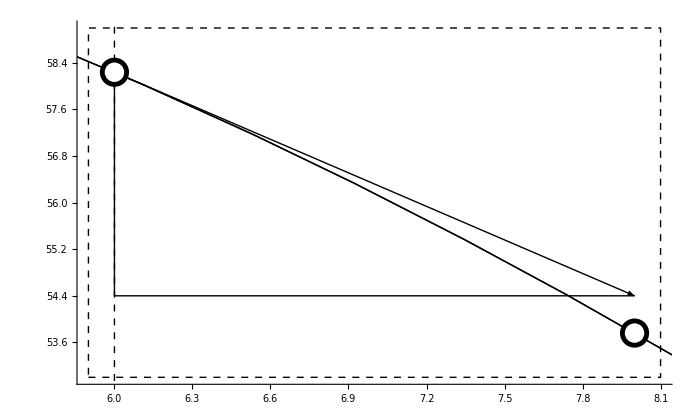

```mathematica
r[t_] = {10t,64-16t^2};
pic0 = ParametricPlot[r[t],{t,0,2},AspectRatio->0.6,PlotStyle->{Thick,Black}];
pts = Cases[pic0,Line[pts_] :> pts[[;;126]],Infinity];
gravity = Table[Arrow[{{x,y},{x,y-20}}],{x,2,20,4},{y,30,60,30}];
brokenTrajectory = Show[pic0,ImageSize->700,
PlotRange -> {{0,30},{0,70}},
Prolog -> { Dashed,Arrowheads[0.015],gravity},
Epilog->{
Arrow[pts],
{Arrowheads[0.02],Arrow[{r[3/5],r[3/5]+0.2*r'[3/5]}]},
Line[{r[3/5],{r[3/5][[1]],(r[3/5]+r'[3/5]/5)[[2]]},r[3/5]+r'[3/5]/5}],
{Black,PointSize[0.012],Table[Point[r[t]],{t,0,2,1/5}]},
{White,PointSize[0.008],Table[Point[r[t]],{t,0,2,1/5}]},
{Dashed,Line[{{5.9,53},{8.1,53},{8.1,59},{5.9,59},{5.9,53}}]}
}];
inset = Show[brokenTrajectory, PlotRange->{{5.9,8.1},{53,59}}, PlotRangePadding->0.01];
busyTrajectory = Show[{brokenTrajectory, 
Graphics[{Inset[inset,{20,67}, {7,57}, 14, Background->White],
Text[MaTeX["W_i \\approx \\mathbf{F}(\\mathbf{r}(t_i))\\cdot\\mathbf{r}'(t_i)\\Delta t",FontSize->20], {22,69}],
{Dashed,Gray,
Line[{{5.9,59},{13,81}}],
Line[{{5.9,53},{13,38}}]
},
{Arrowheads[Medium],Arrow[{{3,-10},{18,-10}}],Text[MaTeX["t", FontSize->18],{18.5,-10}],
{Thickness[0.001],Line[{{4,-9},{4,-11}}],Line[{{16,-9},{16,-11}}]}},
{Black,PointSize[0.01],Table[Point[{x,-10}],{x,4,16,12/10}]},
{White,PointSize[0.007],Table[Point[{x,-10}],{x,4,16,12/10}]},
{Text[MaTeX["t=0", FontSize -> 16],{4,-13}],Text[MaTeX["t=2", FontSize -> 16],{16,-13}]}
}] /. 
{Arrowheads[0.02] -> Arrowheads[0.05],
PointSize[0.012] -> PointSize[0.03],
PointSize[0.008]->PointSize[0.02]}
}, PlotRange->{{-2,29},{-15,82}}, PlotRangePadding->None, Ticks -> ticks,
ImageSize -> 800]
```

```mathematica
Export["busyTrajectory.png", busyTrajectory]
```

busyTrajectory.png

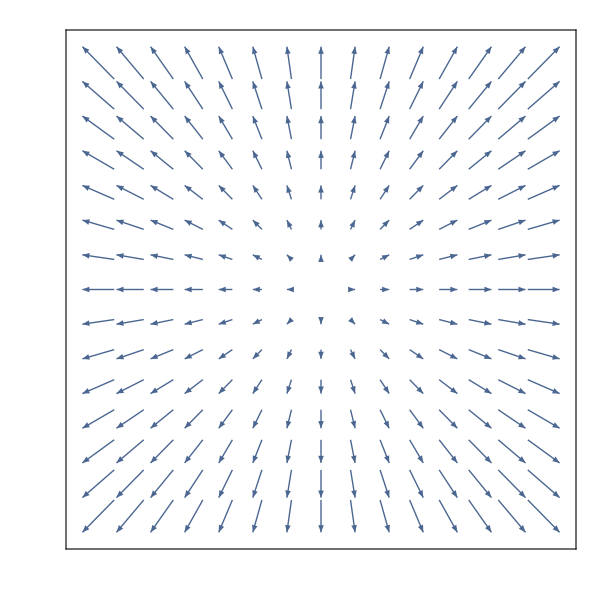

```mathematica
VectorPlot[{x,y},{x,-2,2},{y,-2,2}, ImageSize->600,
FrameTicks -> {{Table[{x,MaTeX[x, FontSize->18]},{x,-2,2}],{}},{Table[{x,MaTeX[x, FontSize->18]},{x,-2,2}],{}}}]
```

```mathematica
Export["identityField.png", %]
```

identityField.png

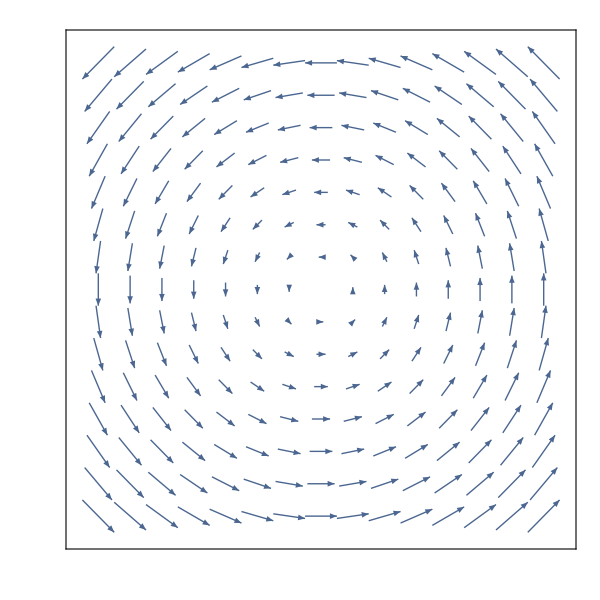

```mathematica
VectorPlot[{-y,x},{x,-2,2},{y,-2,2}, ImageSize->600,
FrameTicks -> {{Table[{x,MaTeX[x, FontSize->18]},{x,-2,2}],{}},{Table[{x,MaTeX[x, FontSize->18]},{x,-2,2}],{}}}]
```

```mathematica
Export["rotationalField.png", %]
```

rotationalField.png

```mathematica
VectorPlot3D[{x,-z,y},{x,-4,4},{y,-2,2},{z,-2,2}, BoxRatios->Automatic, ImageSize->700,
Ticks -> {Table[{x,MaTeX[x]},{x,-4,4,2}],Table[{x,MaTeX[x]},{x,-4,4,2}],Table[{x,MaTeX[x]},{x,-4,4,2}]}]
```

-Graphics3D-

```mathematica
Export["3DField.png", %]
```

3DField.png

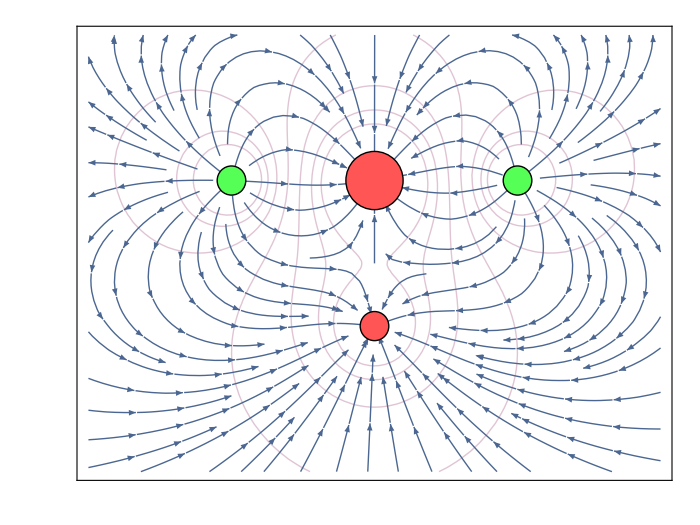

```mathematica
electricField[{q_,r0:{x0_,y0_}}][r:{x_,y_}] := 
With[{v=r-r0},q*v/(v.v)^(3/2)];
q1={-2,{0,1}};
q2={1,{1,1}};
q3={1,{-1,1}};
q4={-1,{0,0}};
charges = {q1,q2,q3,q4};
field = Total[Simplify[electricField[#][{x,y}]& /@ charges]];
electricPotential[{q_,r0:{x0_,y0_}}][r:{x_,y_}] := 
With[{v=r-r0},q/(v.v)^(1/2)];
potential = Total[electricPotential[#][{x,y}]& /@ charges];
point[{q_,p:{x_,y_}}, r_:0.1] := Module[{color},
color = If[q<0,Red,Green];
{{Lighter@color,Disk[p,r*Abs[q]]},Circle[p,r*Abs[q]]}];
cp = ContourPlot[potential, {x,-2,2},{y,-1,2},
ContourShading -> False, ContourStyle -> Directive[Thick,Opacity[0.3],ColorData[1,2]]];
sp = StreamPlot[field, {x,-2,2},{y,-1,2},StreamPoints -> 99];
electro = Show[{cp,sp,Graphics[point /@ charges]}, AspectRatio->Automatic, ImageSize -> 700,
FrameTicks -> {{Table[{x,MaTeX[x, FontSize->18]},{x,-2,2}],{}},{Table[{x,MaTeX[x, FontSize->18]},{x,-2,2}],{}}}]
```

```mathematica
Export["electroStaticField.png", %]
```

electroStaticField.png

```mathematica
Grad[1/Sqrt[x^2+y^2+z^2],{x,y,z}]
```

{-x/((x^2+y^2+z^2)^(3/2)),-y/((x^2+y^2+z^2)^(3/2)),-z/((x^2+y^2+z^2)^(3/2))}

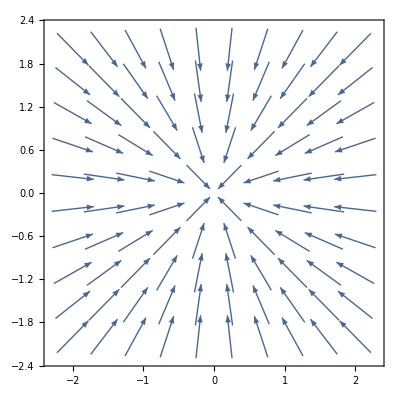

```mathematica
VectorPlot[{-x/(x^2+y^2)^(3/2),-y/(x^2+y^2)^(3/2)},{x,-2,2},{y,-2,2},
VectorScale -> {Automatic,Automatic,1/Norm[{#3,#4}]^(1/15)&},
VectorStyle -> Arrowheads[0.05],
VectorPoints -> 10]
```

```mathematica
Grad[x^2 y^3,{x,y}]
```

{2 x y^3,3 x^2 y^2}

```mathematica
407/354.
```

1.14972

```mathematica
460/400.
```

1.15